# Scattering diagram for McKay quiver

```mathematica
SetDirectory[NotebookDirectory[]];
<<P2Scattering`
<<MaTeX`
```

P2Scattering 1.3 - A package for evaluating DT invariants on K_{P^2}

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.3 - A package for evaluating quiver invariants

```mathematica
With[{x=-1.8},Show[Graphics3D[{Opacity[0.5],InfinitePlane[{{1,1,-2},{1,-2,1},{-2,1,1}}],
InfinitePlane[{{0,0,0},{0,1,0},{0,0,1}}],
InfinitePlane[{{0,0,0},{1,0,0},{0,0,1}}],
InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}],
HalfPlane[{{0,0,0},{1,0,0}},{0,1,-1}],
HalfPlane[{{0,0,0},{1,0,0}},{0,2,-1}],
HalfPlane[{{0,0,0},{1,0,0}},{0,1,-2}],
HalfPlane[{{0,0,0},{0,1,0}},{-1,0,1}],
HalfPlane[{{0,0,0},{0,1,0}},{-2,0,1}],
HalfPlane[{{0,0,0},{0,1,0}},{-1,0,2}],
HalfPlane[{{0,0,0},{0,0,1}},{1,-1,0}],
HalfPlane[{{0,0,0},{0,0,1}},{1,-2,0}],
HalfPlane[{{0,0,0},{0,0,1}},{2,-1,0}],
Opacity[1],Text["γ_1",{0,x,x}],Text["γ_1",{0,-x,-x}],Text["γ_2",{-x,0,-x}],,Text["γ_3",{x,x,0}],Text["γ_3",{-x,-x,0}],
Text["γ_1+γ_2",{-x,x,x}],Text["γ_1+2γ_2",{-x,x/2,x}],
Text["2γ_1+γ_2",{-x/2,x,x}],
Text["γ_2+γ_3",{-x,-x,x}],Text["2γ_2+γ_3",{-x,-x/2,x}],Text["γ_2+2γ_3",{-x,-x,x/2}],
Text["γ_3+γ_1",{x,x,-x}],
Text["γ_3+2γ_1",{x/2,x,-x}],Text["2γ_3+γ_1",{x,x,-x/2}],Text["γ_1+γ_2+γ_3",{-x/2,x/2,0}]}],Axes->True,AxesLabel->{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]},PlotRange->{{-2,2},{-2,2},{-2,2}}]]
```

-Graphics3D-

## Plotting the initial rays and first scatterings

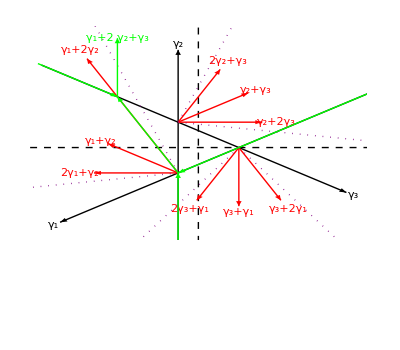

```mathematica
Show[McKayInitialRays[1.5],Graphics[{Red,Thick,
McKayRay[{1,1,0},{-1/2,-Sqrt[3]/2},{0,1},"γ_1+γ_2"],
McKayRay[{1,2,0},{-1/2,-Sqrt[3]/2},{0,1.3},"γ_1+2γ_2"],
McKayRay[{2,1,0},{-1/2,-Sqrt[3]/2},{0,.6},"2γ_1+γ_2"],
McKayRay[{0,1,1},{-1/2,Sqrt[3]/2},{0,1},"γ_2+γ_3"],
McKayRay[{0,1,2},{-1/2,Sqrt[3]/2},{0,.6},"γ_2+2γ_3"],
McKayRay[{0,2,1},{-1/2,Sqrt[3]/2},{0,.6},"2γ_2+γ_3"],
McKayRay[{1,0,1},{1,0},{0,1},"γ_3+γ_1"],
McKayRay[{1,0,2},{1,0},{0,.6},"γ_3+2γ_1"],
McKayRay[{2,0,1},{1,0},{0,.6},"2γ_3+γ_1"],
Purple,Dotted,
McKayRay[{2,3+Sqrt[5],0},{-1/2,-Sqrt[3]/2},{0,1},""],McKayRay[{2,3-Sqrt[5],0},{-1/2,-Sqrt[3]/2},{0,2},""],McKayRay[{0,2,3+Sqrt[5]},{-1/2,Sqrt[3]/2},{0,1},""],McKayRay[{0,2,3-Sqrt[5]},{-1/2,Sqrt[3]/2},{0,2},""],
McKayRay[{2,0,3+Sqrt[5]},{1,0},{0,1},""],
McKayRay[{2,0,3-Sqrt[5]},{1,0},{0,2},""]}],
McKayScattDiag[McKayTrees[{1,2,1}]],PlotRange->{{-4,4},{-3,4}}]
```

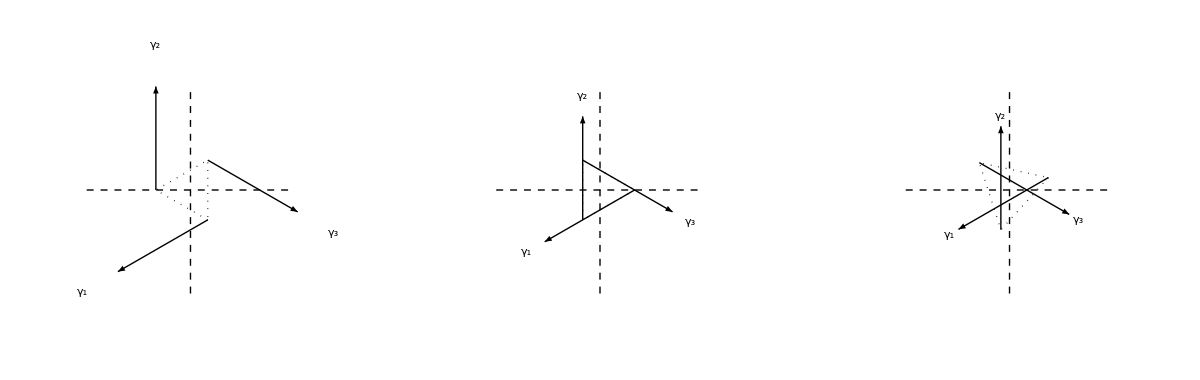

```mathematica
(* Rays start at finite distance in the full scattering diagram: *) 
Show[GraphicsGrid[{{McKayInitialRays[0,1/4],McKayInitialRays[-CriticalPsi[1/2],1/2],McKayInitialRays[-1.5CriticalPsi[1/2],1]}}]]
```

## Scattering diagrams for Hilbert scheme of n points: dim vector {n-1,n,n}

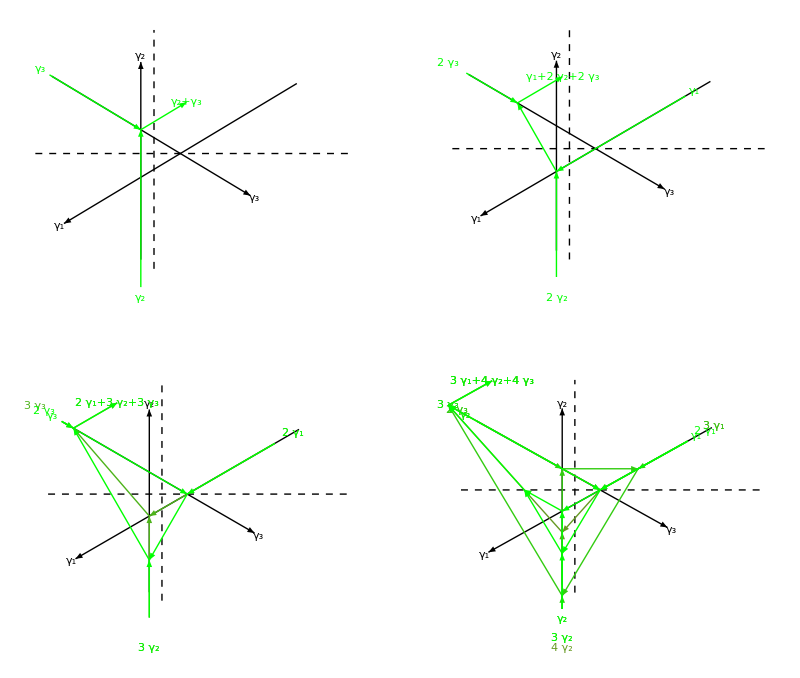

```mathematica
GraphicsGrid[{{Show[McKayInitialRays[1.5],McKayScattDiag[McKayTrees[{0,1,1}]]],Show[McKayInitialRays[1.5],McKayScattDiag[McKayTrees[{1,2,2}]]]},{Show[McKayInitialRays[1.5],McKayScattDiag[McKayTrees[{2,3,3}]]],Show[McKayInitialRays[1.5],McKayScattDiag[McKayTrees[{3,4,4}]]]}}]
```

## Finding all trees contributing in anti-attractor chamber

Constructing the trees for (r,d,chi)={1,1,-1}

{{γ_1,{3 γ_2,4 γ_3}},{{γ_1,3 γ_2},4 γ_3},{{{γ_1,2 γ_2},4 γ_3},γ_2},{{{γ_1,2 γ_2},3 γ_3},{γ_2,γ_3}}}

Index={Kr_3[1,1] Kr_3[3,4],Kr_3[1,3] Kr_6[1,4],Kr_3[1,2] Kr_3[1,4] Kr_9[1,1],Kr_3[1,1]^2 Kr_3[1,2] Kr_3[1,3]}

{204,15,0,27}

{y^14+2 y^12+5 y^10+9 y^8+16 y^6+23 y^4+30 y^2+32+O[1/y]^1,y^8+y^6+2 y^4+2 y^2+3+O[1/y]^1,0,y^6+3 y^4+6 y^2+7+O[1/y]^1}

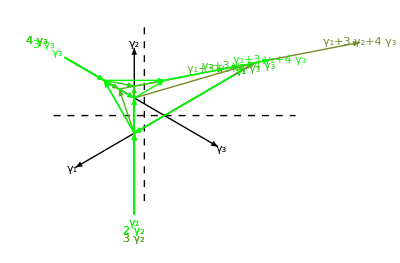

```mathematica
With[{n1=1,n2=3,n3=4},
Print["Constructing the trees for (r,d,chi)=",ntochi[{n1,n2,n3}]];
LiTrees=McKayScanAllTrees[{n1,n2,n3}];
Print[LiTrees/.McKayrep];
IndKr=McKayScattIndex[LiTrees];
Print["Index=",IndKr];
Ind=EvaluateKronecker[IndKr];
Print[Limit[Ind,y->1]];
Print[Series[Ind,{y,Infinity,0}]];
Show[McKayInitialRays[1.5],McKayScattDiag[LiTrees]]
]
```

```mathematica
(* When some internal charges are non-primitive, more care is needed to compute the index : *)L21=TropicalVertex[3,{2,1},{y^2+1+1/y^2,-y^5-y^3-y-1/y-1/y^3-1/y^5},{1}];
L22=TropicalVertex[3,{2,2},{y^2+1+1/y^2,-y^5-y^3-y-1/y-1/y^3-1/y^5},{1}];
L31=TropicalVertex[3,{3,1},{y^2+1+1/y^2,-y^5-y^3-y-1/y-1/y^3-1/y^5,y^10+y^8+2y^6+2y^4+2y^2+2+2/y^2+2/y^4+2/y^6+1/y^8+1/y^10},{1}];
IndModif=IndKr/.{Subscript[Kr, 3][2,2]^2->l22,Subscript[Kr, 3][2,2]->l21/Subscript[Kr, 3][1,2] , Subscript[Kr, 3][3,3]->l31/Subscript[Kr, 3][1,3]};
Ind=EvaluateKronecker[IndModif]/.{l21->L21,l31->L31,l22->L22};
Limit[Ind,y->1]
Series[Ind,{y,Infinity,0}]
```

{3}

{y^2+1+O[1/y]^1}